## Get helper functions

```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"UTILITY_readBeamFiles.nb"}]]
```

## Import

```mathematica
(*fileName= FileNameJoin[{NotebookDirectory[],"beams","nmmToL0AFEND_2bunch_2024-02-16Clean","2024-02-16_2bunch_1e5Downsample_nudgeWeights.h5"}];*)

fileName= FileNameJoin[{NotebookDirectory[],"optimizerRunningBestBeam_MFFF.h5"}];

(*fileName= FileNameJoin[{NotebookDirectory[],"beams","2024-10-14_Impact_TwoBunch","2024-10-14_twoBunch.h5"}];*)

(*fileName  = "/Users/nmajik/Downloads/PENT_moversOnly.h5";*)

data = readBeamFile[fileName];
(*{driverData,witnessData} = getDriverAndWitness[data];*)
```

## Visualize

```mathematica
densityHistogramMod[10^6{#x,#px/#pz}&/@data,{200,200},LabelStyle->20,ImageSize->800]
(*densityHistogramMod[{#x,#px/#pz}&/@driverData,{100,100}(*,LabelStyle->20,ImageSize->800*)]
densityHistogramMod[{#x,#px/#pz}&/@witnessData,{100,100}(*,LabelStyle->20,ImageSize->800*)]*)
```

-Graphics-

```mathematica
densityHistogramMod[{#t,#pz}&/@data,{100,100}(*,LabelStyle->20,ImageSize->800*)]
```

-Graphics-

48.1015

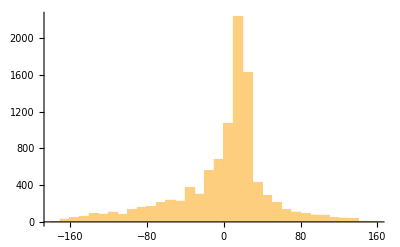

```mathematica
StandardDeviation[10^6 data[[All,"z"]]]
Histogram[10^6 data[[All,"z"]]]
```

```mathematica
ListPointPlot3D[{#x,#px/#pz,#pz}&/@data,SphericalRegion->True,ImageSize->800,ColorFunction->"Rainbow",BoxRatios->{1,1,1}]
```

-Graphics3D-